```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jinyunlin/QFE-Research/affineFlow-2/JintestCode/testing/ConstantLattice

```mathematica
affineplane[r1_, r2_, N_, a_]:=Table[Table[i*r1*a+j*r2*a, {j, -N,N}], {i, -N,N}];

ProjectToSphere[x_]:={x[[1]]/(1+Dot[x,x]), x[[2]]/(1+Dot[x,x]),(-1+Dot[x,x])/(2+2*Dot[x,x])}
ProjectToPlane[x_]:={x[[1]]/(1/2-x[[3]]), x[[2]]/(1/2-x[[3]])}
```

```mathematica
r1 = {0,1}; 
r2 = {1/2,Sqrt[3]/2}; 

NN = 10; 
a = 0.01;
```

```mathematica
Spherepos = ProjectToSphere/@Flatten[affineplane[r1,r2,NN,a], 1];
```

```mathematica
rvec = Import["CurvedTriangleupdate_8_final.dat"][[All, {3,4,5}]];
```

```mathematica
tangentPlant = ProjectToPlane/@rvec;
```

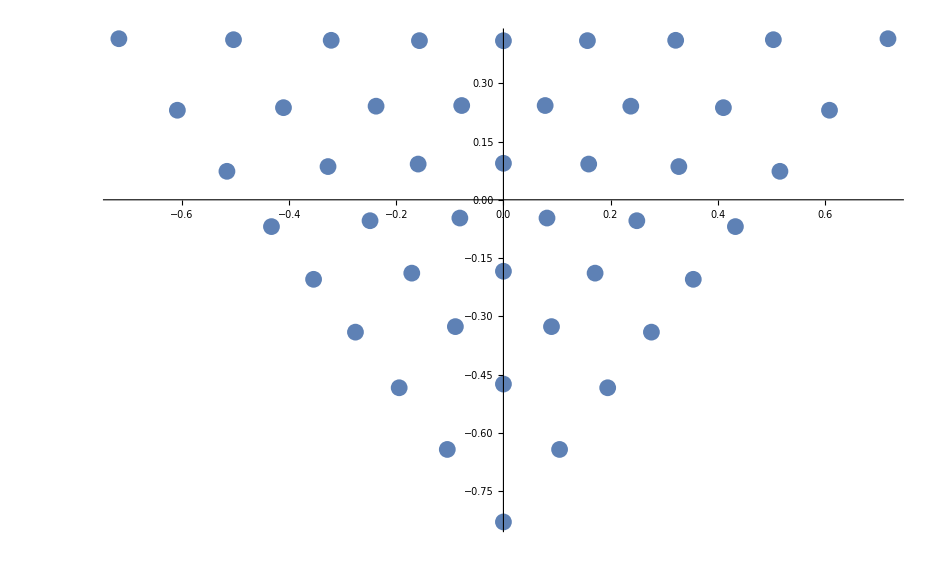

```mathematica
ListPlot[tangentPlant]
```

```mathematica
Graphics3D[{PointSize[Large],Point[Spherepos]},Boxed->True,Axes->True]
```

-Graphics3D-

```mathematica
triangle[N_]:=Module[{points, fullList={}, target, Triangles,dx, dy, dz},
points= Flatten[Table[Table[{i,j}, {j, 1,2*N+1}], {i, 1,2*N+1}], 1];
{dx,dy, dz}= {{0,1}, {1,0}, {-1,1}}; 
Reap[Do[
target = points[[i]];
(*Print[target];*)
Triangles = {{target, target+dx, target+dy},{target, target+dy, target+dz},{target, target+dz, target-dx},{target, target-dx, target-dy},{target, target-dy, target-dz},{target, target-dz, target+dx} }; 
(*Print[Triangles[[2]]];*)
Do[If[SubsetQ[points,Triangles[[j]]],Sow[Triangles[[j]]]],{j,6}]
,{i, Length[points]}]][[2,1]]
]
Ttriangle[N_]:=Module[{points, fullList={}, target, Triangles,dx, dy, dz},
points= Flatten[Table[Table[{i,j}, {j, 1, N+1-i}], {i, 1, N+1}], 1];
{dx,dy, dz}= {{0,1}, {1,0}, {-1,1}}; 
Reap[Do[
target = points[[i]];
(*Print[target];*)
Triangles = {{target, target+dx, target+dy},{target, target+dy, target+dz},{target, target+dz, target-dx},{target, target-dx, target-dy},{target, target-dy, target-dz},{target, target-dz, target+dx} }; 
(*Print[Triangles[[2]]];*)
Do[If[SubsetQ[points,Triangles[[j]]],Sow[Triangles[[j]]]],{j,6}]
,{i, Length[points]}]][[2,1]]
]
A[r1_, r2_, r3_]:=Module[{l1, l2, l3}, 
l1 = Dot[r1-r2, r1-r2];
l2 = Dot[r1-r3, r1-r3];
l3 = Dot[r3-r2, r3-r2];
Sqrt[2l1*l2+2l1*l3+2l2*l3 - l2^2-l1^2-l3^2]/4
]
P[r1_, r2_, r3_]:=Module[{l1, l2, l3}, 
l1 = Dot[r1-r2, r1-r2];
l2 = Dot[r1-r3, r1-r3];
l3 = Dot[r3-r2, r3-r2];
Sqrt[l1]+Sqrt[l2]+Sqrt[l3]
]
Cr[r1_, r2_, r3_]:=Module[{l1, l2, l3}, 
l1 = Dot[r1-r2, r1-r2];
l2 = Dot[r1-r3, r1-r3];
l3 = Dot[r3-r2, r3-r2];
Sqrt[l1*l2*l3]/(4*A[r1,r2,r3])
]
```

```mathematica
Ttriangle[3]
```

{{{1,1},{1,2},{2,1}},{{1,2},{1,3},{2,2}},{{1,2},{2,1},{1,3}},{{2,1},{2,2},{3,1}},{{2,1},{3,1},{1,2}},{{2,2},{1,3},{2,1}},{{2,2},{2,1},{1,2}},{{2,2},{1,2},{3,1}}}

```mathematica
L=10; 
r1 = {0,1}; 
r2 = {1,0}; 
a = 0.005;
```

```mathematica
dataArray = affineplane[r1,r2,L,a];
triangleList=triangle[L];
triangleData=Map[dataArray[[#[[1]],#[[2]]]]&,triangleList,{2}];
pos= Map[ProjectToSphere[#]&, triangleData, {2}];
Areaterm = A[#[[1]], #[[2]], #[[3]]]&/@Map[ProjectToSphere[#]&, triangleData, {2}]//N;
res = Table[{pos[[i]], Areaterm[[i]]},{i, Length[Areaterm]}];
```

```mathematica
minValue=Min[Areaterm];
maxValue=Max[Areaterm];
scaledColorFunction[value_]:=ColorData["Rainbow"][(value-minValue)/(maxValue-minValue)];
heatMap=Graphics3D[{EdgeForm[],{scaledColorFunction[#[[2]]],Polygon[#[[1]]]}&/@res},Axes->True];
legend=BarLegend[{"Rainbow",{minValue,maxValue}}];
fig=Legended[heatMap,legend]
```

-Graphics3D-